```mathematica
Δt:=100 ; 
Ig[t_]:=ⅇ^(-4Log[2](t/Δt)^2) (*gaussian pulse intensity. FWHM=Δt*)
Is[t_]:=Sech[1.763 t/Δt]^2(*sech^2 pulse intensity. FWHM=Δt*)
```

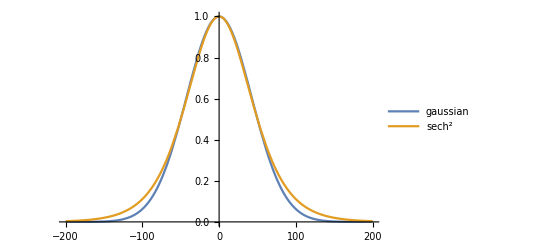

```mathematica
Plot[{Ig[t],Is[t]},{t,-200,200},PlotLegends->{"gaussian","sech^2"}]
```

```mathematica
Ig[50.]
Is[50.]
```

0.5

0.499911

```mathematica
(*Autocorrelations*)
ACg[τ_]=Integrate[Ig[t]Ig[t-τ],{t,-∞,∞}];
ACs[τ_?NumericQ]:=NIntegrate[Is[t]Is[t-τ],{t,-∞,∞}];(*'?NumericQ' is for delaying the numerically evaluation*)
```

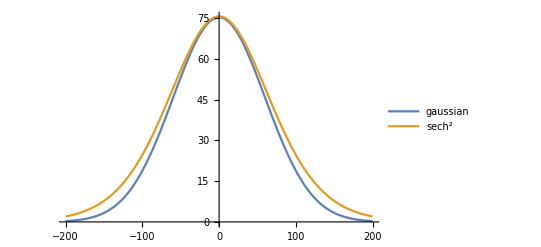

```mathematica
Plot[{ACg[τ],ACs[τ]},{τ,-200,200},PlotLegends->{"gaussian","sech^2"}]
```

```mathematica
sol=FindRoot[ACg[x]-0.5ACg[0],{x,Δt/2}](*find the gaussian's AC HWHM*)
Δt/(2*x/.sol)(*pulse FWHM / AC FWHM*)
```

{x→70.7107}

0.707107

```mathematica
sol=FindRoot[ACs[x]-0.5 ACs[0],{x,Δt/2}](*find the sech^2's AC HWHM*)
Δt/(2*x/.sol)(*pulse FWHM / AC FWHM*)
```

{x→77.1295}

0.648261

```mathematica
0.65*6*1.4/1.62*50
```

168.519